```mathematica
<<FormsAndVectors`
```

```mathematica
r=1;(*radius*)
```

```mathematica
paraMap = r{Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]} ;(*parametric map*)
```

```mathematica
$Assumptions=0<u&&u<π&&0≤v&&v<2π
```

0<u&&u<π&&0≤v&&v<2 π

```mathematica
repRules = {Cot[u]->z/Sqrt[1-z^2],Cos[u]->z,Sin[u]->Sqrt[1-z^2],Sin[v]->y/Sqrt[1-z^2],Cos[v]->x/Sqrt[1-z^2]}
```

{Cot[u]→z/(√(1-z^2)),Cos[u]→z,Sin[u]→√(1-z^2),Sin[v]→y/(√(1-z^2)),Cos[v]→x/(√(1-z^2))}

```mathematica
g=MetricFromPara[paraMap,u,v] //Simplify (*getMetric*)
```

{{1,0},{0,Sin[u]^2}}

```mathematica
muVal = Sqrt[Det[g]]//Simplify
```

Sin[u]

```mathematica
fz=paraMap[[3]]//Simplify
```

Cos[u]

```mathematica
rotz = Rot0[fz,u,v,g]//Simplify
```

{0,-Sin[u]^2}

```mathematica
dz = ExD0[fz,u,v]//Simplify
```

{-Sin[u],0}

```mathematica
LCoBeltrami1[dz,u,v,g]//Simplify
```

{2 Sin[u],0}

```mathematica
alpha = rotz + dz //FullSimplify
```

{-Sin[u],-Sin[u]^2}

```mathematica
L2Prod1[alpha,alpha,{u,0,π},{v,0,2π},g]
```

(16 π)/3

```mathematica
rotalpha = Rot1[alpha,u,v,g]//Simplify
```

-2 Cos[u]

```mathematica
L2Prod0[rotalpha,rotalpha,{u,0,π},{v,0,2π},g]
```

(16 π)/3

```mathematica
divalpha = -ExCoD1[alpha,u,v,g]//Simplify
```

-2 Cos[u]

```mathematica
L2Prod0[divalpha,divalpha,{u,0,π},{v,0,2π},g]
```

(16 π)/3

```mathematica
rotzR3=GlobalVecFromPara[Sharp1[rotz,g],paraMap, u, v]/.repRules//Simplify
dzR3=GlobalVecFromPara[Sharp1[dz,g],paraMap, u, v]/.repRules//Simplify
```

{y,-x,0}

{-x z,-y z,1-z^2}

```mathematica
norm2dzdz= DotForm1[dz,dz,g]*dz//Simplify
```

{-Sin[u]^3,0}

```mathematica
norm2dzdzR3=GlobalVecFromPara[Sharp1[norm2dzdz,g],paraMap, u, v]/.repRules//FullSimplify
```

{x z (-1+z^2),y z (-1+z^2),(-1+z^2)^2}

```mathematica
floc=Integrate[-(2Sin[u]+ Sin[u]^3),u]//Simplify//TrigExpand
```

(11 Cos[u])/4-Cos[u]^3/12+1/4 Cos[u] Sin[u]^2

```mathematica
fglob=floc/.repRules//FullSimplify
```

-1/3 z (-9+z^2)

```mathematica
h=paraMap[[3]]*(3-paraMap[[3]]^2/3)//FullSimplify
```

-1/3 Cos[u] (-9+Cos[u]^2)

```mathematica
h-floc//Simplify
```

0

```mathematica
dh=ExD0[h,u,v]//FullSimplify
```

{(-3+Cos[u]^2) Sin[u],0}

```mathematica
fzzz = fz - ϵ*Sqrt[1-fz^2]//Simplify
```

Cos[u]-ϵ Sin[u]

```mathematica
dzzz=ExD0[fzzz,u,v]//Simplify
```

{-ϵ Cos[u]-Sin[u],0}

```mathematica
norm2dzzz=DotForm1[dzzz,dzzz,g]//Simplify
```

(ϵ Cos[u]+Sin[u])^2

```mathematica
norm2dzzzR3=norm2dzzz/.repRules//FullSimplify
```

(√(1-z^2)+z ϵ)^2

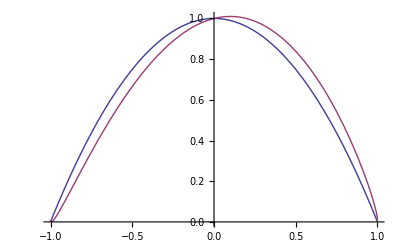

```mathematica
Plot[{1-z^2,norm2dzzzR3/.ϵ->0.1},{z,-1,1}]
```

```mathematica
fxyz=paraMap[[1]]*paraMap[[2]]*paraMap[[3]]
fx=paraMap[[1]]
```

Cos[u] Cos[v] Sin[u]^2 Sin[v]

Cos[v] Sin[u]

```mathematica
dxyz=ExD0[fxyz,u,v]//Simplify
dx=ExD0[fx,u,v]//Simplify
```

{1/4 (1+3 Cos[2 u]) Sin[u] Sin[2 v],Cos[u] Cos[2 v] Sin[u]^2}

{Cos[u] Cos[v],-Sin[u] Sin[v]}

```mathematica
dxyzdx=Dot1[dxyz,dx,g]//Simplify//TrigExpand
```

5/8 Cos[u] Sin[u] Sin[v]+3/8 Cos[u]^3 Sin[u] Sin[v]-9/8 Cos[u] Cos[v]^2 Sin[u] Sin[v]+9/8 Cos[u]^3 Cos[v]^2 Sin[u] Sin[v]-3/8 Cos[u] Sin[u]^3 Sin[v]-9/8 Cos[u] Cos[v]^2 Sin[u]^3 Sin[v]+3/8 Cos[u] Sin[u] Sin[v]^3-3/8 Cos[u]^3 Sin[u] Sin[v]^3+3/8 Cos[u] Sin[u]^3 Sin[v]^3

```mathematica
rhs=GlobalVecFromPara[Sharp1[dxyzdx*dz+2dz,g], paraMap, u, v]/.repRules//Simplify//TrigExpand
```

{-2 x z-1/4 x y z^2+9/4 x^3 y z^2-3/4 x y^3 z^2-3/4 x y z^4,-2 y z-(y^2 z^2)/4+9/4 x^2 y^2 z^2-(3 y^4 z^2)/4-(3 y^2 z^4)/4,2+(y z)/4-9/4 x^2 y z+(3 y^3 z)/4-2 z^2+(y z^3)/2+9/4 x^2 y z^3-(3 y^3 z^3)/4-(3 y z^5)/4}

```mathematica
rhs//FullSimplify
```

{1/4 x z (-8-y z (1-9 x^2+3 y^2+3 z^2)),-1/4 y z (8+y z (1-9 x^2+3 y^2+3 z^2)),-1/4 (-1+z^2) (8+y z (1-9 x^2+3 y^2+3 z^2))}

```mathematica
dxyzdx+2/.repRules//Simplify//TrigExpand//Simplify
```

1/4 (8+3 y^3 z+y (z-9 x^2 z+3 z^3))

```mathematica
%//FullSimplify
```

1/4 (8+y z (1-9 x^2+3 y^2+3 z^2))

```mathematica
beta=(dxyzdx+2)dz//FullSimplify
```

{1/16 Sin[u] (-32-(13 Cos[u]+3 Cos[3 u]) Sin[u] Sin[v]+12 Cos[u] Sin[u]^3 Sin[3 v]),0}

```mathematica
bfun=Integrate[beta[[1]],u]//FullSimplify//TrigExpand
```

2 Cos[u]-5/32 Sin[u] Sin[v]+7/64 Cos[u]^2 Sin[u] Sin[v]+3/64 Cos[u]^4 Sin[u] Sin[v]+9/32 Cos[v]^2 Sin[u] Sin[v]-27/64 Cos[u]^2 Cos[v]^2 Sin[u] Sin[v]+9/64 Cos[u]^4 Cos[v]^2 Sin[u] Sin[v]-7/192 Sin[u]^3 Sin[v]-3/32 Cos[u]^2 Sin[u]^3 Sin[v]+9/64 Cos[v]^2 Sin[u]^3 Sin[v]-9/32 Cos[u]^2 Cos[v]^2 Sin[u]^3 Sin[v]+3/320 Sin[u]^5 Sin[v]+9/320 Cos[v]^2 Sin[u]^5 Sin[v]-3/32 Sin[u] Sin[v]^3+9/64 Cos[u]^2 Sin[u] Sin[v]^3-3/64 Cos[u]^4 Sin[u] Sin[v]^3-3/64 Sin[u]^3 Sin[v]^3+3/32 Cos[u]^2 Sin[u]^3 Sin[v]^3-3/320 Sin[u]^5 Sin[v]^3

```mathematica
bfun/.repRules//Simplify//TrigExpand//Simplify
```

1/60 (120 z+9 y^3 (-1+z^2)-y (-11+27 x^2-9 z^2) (-1+z^2))

```mathematica
%//FullSimplify
```

1/60 (120 z+y (-1+z^2) (11-27 x^2+9 y^2+9 z^2))